## Lu163 - Energy Ellipsoid

## Graphical representation for the energy function H in a 3D space

### New formalism for the energy ellipsoid (given by the current expression of the energy function, expressed in terms of the spherical coordinates)

Cartesian to spherical coordinate transformation is required

```mathematica
ellipsoid[a1_,a2_,a3_,e_]:=ContourPlot3D[a1*x^2+a2*y^2+a3*z^2==e*(e+1),{x,-1.2e,1.2e},{y,-1.2e,1.2e},{z,-1.2e,1.2e},ContourStyle->{Orange,Opacity[0.6]},Mesh->None];
```

## Cartesian coordinates

x_1=I sinθ cosφ
x_2=I sinθ sinφ
x_3=I cosθ

## Energy Formulas

The Cartesian expressions

```mathematica
j=13/2;
A1Fit=1/(2*72);
A2Fit=1/(2*15);
A3Fit=1/(2*7);
IF[X_]:=X;
```

## Numerical data (TSD energies)

```mathematica
e0=1.7399;
spin1=Table[8.5+2i,{i,0,20}];
spin2=Table[13.5+2i,{i,0,16}];
spin3=Table[16.5+2i,{i,0,13}];
spin4=Table[23.5+2i,{i,0,9}];
(*excitation  energies*)
tsd1={0.230329,0.516162,0.857522,1.25441,1.70683,2.21478,2.77826,3.39726,4.07178,4.80183,5.5874,6.42849,7.3251,8.27724,9.28491,10.3481,11.4668,12.6411,13.8708,15.1561,16.497};
tsd2={1.34903,1.77368,2.25387,2.78958,3.38082,4.02758,4.72986,5.48767,6.301,7.16986,8.09423,9.07413,10.1096,11.2005,12.347,13.549,14.8065};
tsd3={2.04238,2.57396,3.15888,3.7974,4.48976,5.23613,6.0367,6.89161,7.80099,8.76495,9.7836,10.857,11.9853,13.1685};
tsd4={4.32758,5.02986,5.78767,6.601,7.46986,8.39423,9.37413,10.4096,11.5005,12.647};
(*absolute energies*)
tsd1Abs=tsd1+e0;
tsd2Abs=tsd2+e0;
tsd3Abs=tsd3+e0;
tsd4Abs=tsd4+e0;
```

## Energy function in Cartesian coordinates

(1-1/(2I))A1*x_1^2+(1-1/(2I))A2*x_2^2+((1-1/(2I))A3+A1*j/I)x_3^2+I/2(A1+A2)+A3*I^2+j/2(A2+A3)+A1*j^2-I(I-1/2)A3-2*A1*I*j

## 3D-Figures

### Determine the scaling for the ellipsoid dynamically

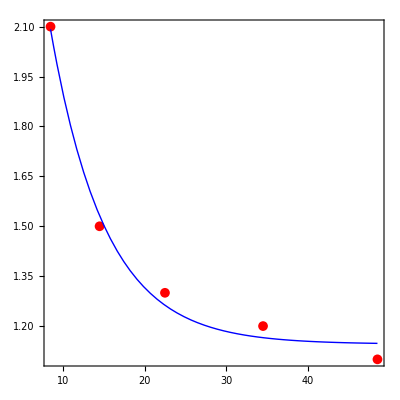

```mathematica
scaleEvolution={{spin1[[1]],2.1},{spin1[[4]],1.5},{spin1[[8]],1.3},{spin1[[14]],1.2},{spin1[[21]],1.1}};
fit=FindFit[scaleEvolution,a*Exp[-b*x]+c,{a,b,c},x,Method->NMinimize];
Show[ListPlot[scaleEvolution,Frame->True,Axes->False,PlotStyle->Red,PlotMarkers->{Automatic, Medium},AspectRatio->1],Plot[(a*Exp[-b*x]+c)/.fit,{x,spin1[[1]],spin1[[Length[spin1]]]},PlotStyle->{Blue,Thick}],PlotRange->Full]
```

```mathematica
(*extra padding for the sphere's radius*)
pad=1.5;
LuEllipsoid[I_,e_,A1_,A2_,A3_]:=ContourPlot3D[(1-1/(2I))A1*x^2+(1-1/(2I))A2*y^2+((1-1/(2I))A3+A1*j/I)z^2+I/2(A1+A2)+A3*I^2+j/2(A2+A3)+A1*j^2-I(I-1/2)A3-2*A1*I*j==e,{x,-2.1*I,2.1*I},{y,-2.1*I,2.1*I},{z,-2.1*I,2.1*I},ContourStyle->{Blue,Opacity[0.5]},Mesh->None,PlotPoints->50];
sphere[I_,e_,A1_,A2_,A3_]:=ContourPlot3D[x^2+y^2+z^2==I*(I+1),{x,-(I+pad),(I+pad)},{y,-(I+pad),(I+pad)},{z,-(I+pad),(I+pad)},MeshFunctions->{Function[{x,y,z},Evaluate[(1-1/(2I))A1*x^2+(1-1/(2I))A2*y^2+((1-1/(2I))A3+A1*j/I)z^2+I/2(A1+A2)+A3*I^2+j/2(A2+A3)+A1*j^2-I(I-1/2)A3-2*A1*I*j]]},Mesh->{{e}},ContourStyle->{Red,Specularity[0.2],Opacity[0.8]},MeshStyle->{Yellow,Thick},PlotPoints->50,BoundaryStyle->None,Boxed->False,Axes->False];
axes[I_,e_,axscale_]:={Graphics3D[{Thick,Black,Arrow[{{0,0,0},{0,0,I+axscale}}],Inset[Style["x_3",20,Bold,Italic,FontFamily->"Times New Roman"],Scaled[{0,0,.1},{0,0,I+axscale}]]},Boxed->False,PlotLabel->Style[StringTemplate["I=`` ℏ ; E=`` MeV"][I,e],Bold,Italic,Black,18,FontFamily->"Times New Roman"]],Graphics3D[{Thick,Blue,Arrow[{{0,0,0},{I+axscale,0,0}}],Inset[Style["x_1",20,Bold,Italic,FontFamily->"Times New Roman"],Scaled[{0.1,0,0},{I+axscale,0,0}]]}],Graphics3D[{Thick,Black,Arrow[{{0,0,0},{0,I+axscale,0}}],Inset[Style["x_2",20,Bold,Italic,FontFamily->"Times New Roman"],Scaled[{0,0.1,0},{0,I+axscale,0}]]}]};
```

```mathematica
Manipulate[Show[axes[spin1[[k]],tsd1Abs[[k]],axscale],sphere[spin1[[k]],tsd1Abs[[k]],IF[A1Fit],IF[A2Fit],IF[A3Fit]],LuEllipsoid[spin1[[k]],tsd1Abs[[k]],IF[A1Fit],IF[A2Fit],IF[A3Fit]]],{axscale,1,15,1},{k,1,Length[tsd1Abs],1}]
```

```mathematica
(*Manipulate[LuEllipsoid[spin1[[p]],tsd1Abs[[p]],IF[A1Fit],IF[A2Fit],IF[A3Fit],k],{k,1,10,0.1},{p,1,Length[tsd1Abs],1}]*)
```

## Export graphs to file

```mathematica
path="/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Energy_Ellipsoids/";
export[name_,plot_]:=Export[StringTemplate["``.pdf"][StringJoin[path,name]],plot];
```

## TSD1

```mathematica
(*Table[export[StringTemplate["/tsd1/tsd1_ellipsoid_``"][i],Show[axes[spin1[[i]],tsd1Abs[[i]],15],sphere[spin1[[i]],tsd1Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]],LuEllipsoid[spin1[[i]],tsd1Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]]]],{i,1,21,1}];*)
```

## TSD2

```mathematica
(*Table[export[StringTemplate["/tsd2/tsd2_ellipsoid_``"][i],Show[axes[spin2[[i]],tsd2Abs[[i]],15],sphere[spin2[[i]],tsd2Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]],LuEllipsoid[spin2[[i]],tsd2Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]]]],{i,1,17,1}];*)
```

## TSD3

```mathematica
(*Table[export[StringTemplate["/tsd3/tsd3_ellipsoid_``"][i],Show[axes[spin3[[i]],tsd3Abs[[i]],15],sphere[spin3[[i]],tsd3Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]],LuEllipsoid[spin3[[i]],tsd3Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]]]],{i,1,14,1}];*)
```

## TSD4

```mathematica
(*Table[export[StringTemplate["/tsd4/tsd4_ellipsoid_``"][i],Show[axes[spin4[[i]],tsd4Abs[[i]],15],sphere[spin4[[i]],tsd4Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]],LuEllipsoid[spin4[[i]],tsd4Abs[[i]],IF[A1Fit],IF[A2Fit],IF[A3Fit]]]],{i,1,10,1}];*)
```